39.8942

5.3991

0.135335

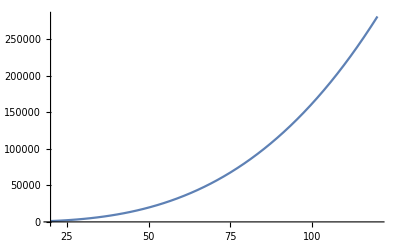

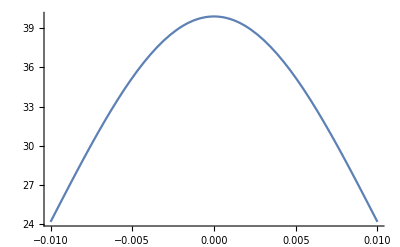

```mathematica
dim = 100;
sigma = 1/dim;
mu = 0;

f[x_]:=1/(Sqrt[2*Pi]*sigma)*Exp[-(x-mu)^2/(2*sigma^2)];
a  = N[f[mu]]
b = N[f[2*sigma]]
b/a
Plot[Binomial[x,3],{x,20,120}]
Plot[f[x],{x,-0.01,0.01}]
```

```mathematica
Solve[(x1-h)^2+(y1-k)^2 -(x3-h)^2 -(y3-k)^2 == 0, {h}]
Solve[(x2-h)^2+(y2-k)^2 -(x3-h)^2 -(y3-k)^2 == 0, {k}]
```

{{h→(x1^2-x3^2-2 k y1+y1^2+2 k y3-y3^2)/(2 (x1-x3))}}

{{k→(-2 h x2+x2^2+2 h x3-x3^2+y2^2-y3^2)/(2 (y2-y3))}}

```mathematica
x1 = 4;
y1 = 1;
x2 = -3;
y2 = 7;
x3 = 5;
y3 = -2;
h =(x1^2-x3^2-2 k y1+y1^2+2 k y3-y3^2)/(2 (x1-x3));
k = (-2 h x2+x2^2+2 h x3-x3^2+y2^2-y3^2)/(2 (y2-y3));
```

```mathematica
Binomial[95,3]-Binomial[80,3]
```

56255